```mathematica
HasProperty[g_,take_]:=Block[{toremove=(take-3)(take-4)/2,vertexCombinations=Subsets[VertexList[g],{take}],h, toremain, result=True},
toremain=(take*(take-1)/2)-toremove;
Table[
h=Subgraph[g,vertexSet];
If[!(EdgeCount[h]<= toremain),
result=False;
Goto[done]
];
,
{vertexSet,vertexCombinations}
];
Label[done];
result
]
```

```mathematica
HasFullProperty[g_]:=Fold[And,Table[HasProperty[g,k],{k,5,VertexCount[g]}]]
```

```mathematica
HasProperty[CompleteGraph[7],6]
```

False

```mathematica
allGr=With[{max=7},
With[{toremove=(max-3)(max-4)/2,
complete=CompleteGraph[7],
allEdges=Map[#[[1]]<->#[[2]]&,Subsets[Range[max],{2}]]},
Table[
EdgeDelete[complete,edges]
,{edges,Subsets[allEdges,{toremove}]}]
]
];
```

```mathematica
Length[allGr]
```

54264

```mathematica
Monitor[Table[{HasProperty[allGr[[k]],7]&&HasProperty[allGr[[k]],6]&&HasProperty[allGr[[k]],5],ChromaticPolynomial[allGr[[k]],4]/24,PlanarGraphQ[allGr[[k]]]},{k,Length[allGr]}],Row[{k,ProgressIndicator[k/Length[allGr]],Length[allGr]}]]//Tally
```

{{{False,0,False},9037},{{False,2,False},4095},{{False,3,False},630},{{True,1,False},3815},{{True,4,False},7245},{{True,1,True},4620},{{True,2,False},14280},{{True,3,False},7700},{{True,7,False},1750},{{True,4,True},840},{{True,5,True},252}}

```mathematica
Map[HasProperty[#,6]&,allGr]//Tally
```

{{False,11662},{True,42602}}

{{{False,0,False},9037},{{False,2,False},4095},{{False,3,False},630},{{True,1,False},3815},{{True,4,False},7245},{{True,1,True},4620},{{True,2,False},14280},{{True,3,False},7700},{{True,7,False},1750},{{True,4,True},840},{{True,5,True},252}}

```mathematica
allGr8=With[{max=8},
With[{toremove=(max-3)(max-4)/2,
complete=CompleteGraph[max],
allEdges=Map[#[[1]]<->#[[2]]&,Subsets[Range[max],{2}]]},
Table[
EdgeDelete[complete,edges]
,{edges,Take[Subsets[allEdges,{toremove}],1000000]}]
]
];Length[allGr8]
```

1000000

```mathematica
Monitor[Fold[And,Table[HasProperty[allGr8[[k]],8],{k,100000}]],Row[{k,ProgressIndicator[k/100000],100000}]]
```

True

```mathematica
ShowGr[g_]:=CompleteGraph[VertexCount[g],GraphHighlight->EdgeList[GraphComplement[g]],VertexLabels->"Name",GraphHighlightStyle->"Thick",ImageSize->300]
```

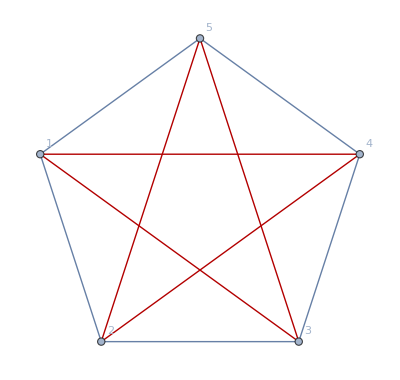

```mathematica
ShowGr[CycleGraph[5]]
```

```mathematica
Tally[Monitor[Table[
With[{prop={HasProperty[allGr8[[k]],7]&&HasProperty[allGr8[[k]],6]&&HasProperty[allGr8[[k]],5],ChromaticPolynomial[allGr8[[k]],4]/24,PlanarGraphQ[allGr8[[k]]],k}},
If[prop [[1]]&&prop[[2]]==0,Print[prop,ShowGr[allGr8[[k]]]]];prop
],{k,452012,Length[allGr8]}],Row[{k,ProgressIndicator[k/Length[allGr8]],Length[allGr8]}]],Most[#]&]//Sort
```

{True,0,False,452012}

{True,0,False,452024}

{True,0,False,452051}

{True,0,False,452071}

{True,0,False,452102}

{True,0,False,452165}

{True,0,False,452171}

{True,0,False,454350}

{True,0,False,454391}

{True,0,False,454646}

{True,0,False,454674}

{True,0,False,455048}

{True,0,False,455054}

{True,0,False,455130}

{True,0,False,455141}

{True,0,False,455148}

{True,0,False,455168}

{True,0,False,455193}

{True,0,False,455209}

{True,0,False,455502}

{True,0,False,455523}

```mathematica
First/@%492
```

{{False,0,False},{False,4,False},{False,3,False},{False,6,False},{False,2,False},{False,17,False},{False,12,False},{False,5,False},{False,9,False},{False,8,False},{False,7,False},{False,16,False},{True,1,False},{True,8,False},{True,2,False},{True,4,False},{True,5,False},{True,13,False},{True,9,False},{True,1,True},{True,3,False},{True,12,False},{True,6,False},{True,7,False},{True,4,True},{True,18,False},{True,10,False},{True,5,True},{True,17,False},{True,11,False}}

```mathematica
Tally[Monitor[Table[
With[{prop={HasProperty[allGr8[[k]],7]&&HasProperty[allGr8[[k]],6]&&HasProperty[allGr8[[k]],5],ChromaticPolynomial[allGr8[[k]],4]/24,PlanarGraphQ[allGr8[[k]]],k}},
If[prop [[1]]&&prop[[2]]==0,Print[prop,ShowGr[allGr8[[k]]]]];prop
],{k,452012,Length[allGr8]}],Row[{k,ProgressIndicator[k/Length[allGr8]],Length[allGr8]}]],Most[#]&]//Sort
```

```mathematica
IsomorphicGraphQ[,]
```